```mathematica
P=y(1+x^2-a y^2);
Q=-x(1-c x^2+y^2);
Simplify[Solve[{P==0,Q==0},{x,y}]]
```

{{x→-1/(√c),y→0},{x→1/(√c),y→0},{x→-(√(1+a))/(√(-1+a c)),y→-(√(1+c))/(√(-1+a c))},{x→-(√(1+a))/(√(-1+a c)),y→(√(1+c))/(√(-1+a c))},{x→(√(1+a))/(√(-1+a c)),y→-(√(1+c))/(√(-1+a c))},{x→(√(1+a))/(√(-1+a c)),y→(√(1+c))/(√(-1+a c))},{x→0,y→0},{x→0,y→-1/(√a)},{x→0,y→1/(√a)}}

```mathematica
P=y(1+x^2-a y^2);
Q=-x(1-c x^2+y^2);
J=({{D[P,x], D[P,y]}, {D[Q,x], D[Q,y]}})
```

{{2 x y,1+x^2-3 a y^2},{-1+3 c x^2-y^2,-2 x y}}

```mathematica
P=y(1+x^2-a y^2);
Q=-x(1-c x^2+y^2);
J=({{D[P,x], D[P,y]}, {D[Q,x], D[Q,y]}});
ID=IdentityMatrix[2];
x=0;y=0;
Solve[{Det[J-λ ID]==0},λ]
```

{{λ→-ⅈ},{λ→ⅈ}}

```mathematica
P=y(1+x^2-a y^2);
Q=-x(1-c x^2+y^2);
J=({{D[P,x], D[P,y]}, {D[Q,x], D[Q,y]}});
ID=IdentityMatrix[2];
x=0;y=1/(√a);
Solve[{Det[J-λ ID]==0},λ]
```

{{λ→-√2 √(1+1/a)},{λ→√2 √(1+1/a)}}

```mathematica
P=y(1+x^2-a y^2);
Q=-x(1-c x^2+y^2);
J=({{D[P,x], D[P,y]}, {D[Q,x], D[Q,y]}});
ID=IdentityMatrix[2];
x=√((1+a)/(-1+a c));y=(√(1+c))/(√(-1+a c));
Simplify[Solve[{Det[J-λ ID]==0},λ]]
```

{{λ→-2 √(((1+a) (1+c))/(1-a c))},{λ→2 √(((1+a) (1+c))/(1-a c))}}

```mathematica
H=y^2/2-(a y^4)/4+x^2/2-(c x^4)/4+(x^2 y^2)/2;
x=√((1+a)/(-1+a c));y=(√(1+c))/(√(-1+a c));
Simplify[H]
```

(2+a+c)/(-4+4 a c)

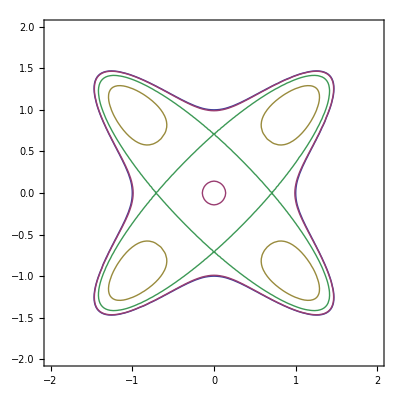

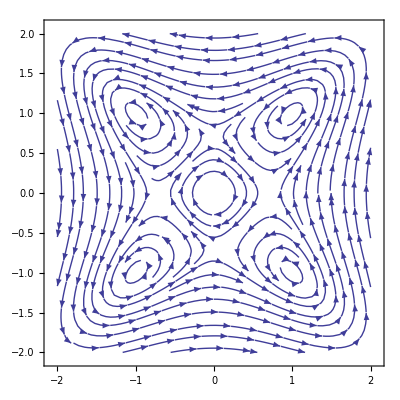

```mathematica
P=y(1+x^2-a y^2);
Q=-x(1-c x^2+y^2);
H=y^2/2-(a y^4)/4+x^2/2-(c x^4)/4+(x^2 y^2)/2;
a=2;c=2;
ContourPlot[{H==0,H==0+1/100,H==0+1/3,H==0+1/8,H==1/(√2)-0.01},{x,-2,2},{y,-2,2}]
StreamPlot[{P,Q},{x,-2,2},{y,-2,2},Axes->True]
```

```mathematica
H=y^2/2-(a y^4)/4+x^2/2-(c x^4)/4+(x^2 y^2)/2;
Plot3D[{H},{x,-1.2,1.2},{y,-1.2,1.2}]
```

-Graphics3D-

```mathematica
a=2;c=10;
H=y^2/2-(a y^4)/4+x^2/2-(c x^4)/4+(x^2 y^2)/2;
Plot3D[{H},{x,-1.2,1.2},{y,-1.2,1.2}]
```

-Graphics3D-

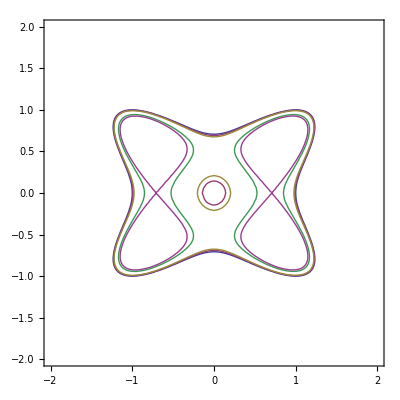

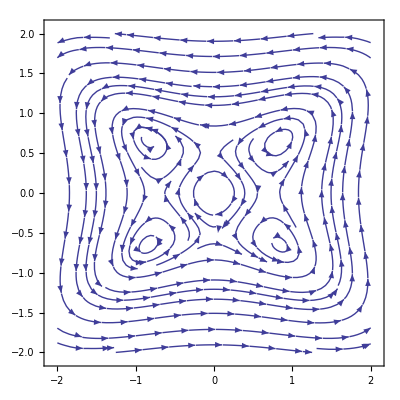

```mathematica
P=y(1+x^2-a y^2);
Q=-x(1-c x^2+y^2);
H=y^2/2-(a y^4)/4+x^2/2-(c x^4)/4+(x^2 y^2)/2;
a=4;c=2;
ContourPlot[{H==0,H==0+1/100,H==0+1/50,H==0+1/10,H==0+1/3,H==0+1/8},{x,-2,2},{y,-2,2}]
StreamPlot[{P,Q},{x,-2,2},{y,-2,2},Axes->True]
```